```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

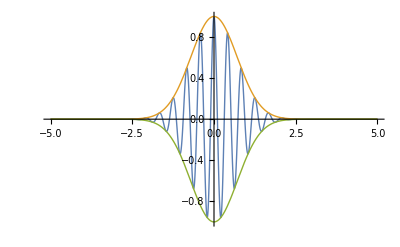

```mathematica
Clear[p, t]
p = Plot[
 Evaluate@Re[{ 
E^(- t^2) E^(15 I t), E^(- t^2), -E^(- t^2)
}], 
{t, -5, 5}, 
PlotStyle->Thick,
PlotRange -> Full, Ticks -> None]
```

```mathematica
peeters`exportForLatex["qmSolidsL19Fig1", p]
```

{qmSolidsL19Fig1.eps,qmSolidsL19Fig1pn.png}

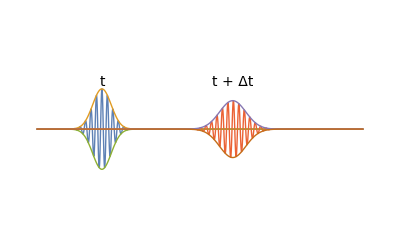

```mathematica
Clear[p]
p = 
Module[{e1, e2, n1, n2, ty},
e1[t_] = E^(- t^2) ;
e2[t_] = E^(- (t-10)^2/2) ;
n1 = Integrate[ e1[t], {t,-Infinity, Infinity}] ;
n2 = Integrate[ e2[t], {t,-Infinity, Infinity}] ;
ty = e1[0]/n1 + 0.1 ;

Plot[ Evaluate@Re[{ 
E^(15 I t) e1[t]/n1,
e1[t]/n1,
-e1[t]/n1,
E^(15 I t) e2[t]/n2,
e2[t]/n2,
-e2[t]/n2
 }], {t, -5, 20}
, PlotRange -> {Full, {-1.1, 1.5}}
, Epilog -> {
Text[ "t"//fs, {0, ty}],
Text[ "t + Δt"//fs, {10, ty}]
}
, AxesLabel-> {t, None}
, PlotStyle->Thick
, Axes -> (*{True, False}*) False
, Ticks -> None ]
]
```

```mathematica
peeters`exportForLatex["qmSolidsL18PacketSpreadingFig1", p]
```

{qmSolidsL18PacketSpreadingFig1.eps,qmSolidsL18PacketSpreadingFig1pn.png}